## Model Setup

```mathematica
wm = ResourceFunction["WolframModel"];
plot = ResourceFunction["WolframModelPlot"];
randomRule = ResourceFunction["RandomWolframModel"];
```

```mathematica
steps=10;
maxValue = 3;
maxVertices=3;
```

```mathematica
randomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
```

```mathematica
signature={{2,2}}->{{4,2}};
init = Array[Function[1],signature[[1]][[1]]];
rule = {{{1,2},{1,3}}->{{1,4},{4,5},{5,2},{3,5}}};
```

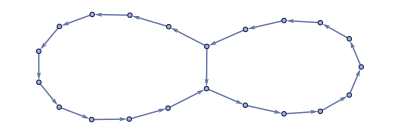

```mathematica
wm[rule, init, steps, "FinalStatePlot"]
```

## Mutations

### Simplest case: retain signature, replace only elements with same range

```mathematica
selectElement[rule_]:=
Module[{replacement, side, edge, vertex, x},
replacement=RandomInteger[{1, Length[rule]}];
x = rule[[replacement]];
side = RandomInteger[{1, 2}];
x = x[[side]];
edge = RandomInteger[{1, Length[x]}];
x = x[[edge]];
vertex = RandomInteger[{1, Length[x]}];
{replacement, side, edge, vertex}
]
```

```mathematica
maxElement[rule_]:=Max[Flatten[List@@@rule]]
```

```mathematica
replaceRandomElement[rule_]:=
Module[{pos=selectElement[rule]},
ReplacePart[rule, pos->
RandomChoice[Delete[Range[1,maxElement[rule]],Extract[rule, pos]]
]]]
```

### Find rules which give connected graphs of increasing dimension

```mathematica
ruleDimension[rule_, nSteps_]:=graphDimension[Graph[wm[rule, {{1,1},{1,1}}, nSteps, "FinalState"]]]
```

```mathematica
graphDimension[graph_] :=
If[ConnectedGraphQ[graph],
 	ResourceFunction["WolframHausdorffDimension"][graph,All, "AllDimensions","VertexMethod" -> Max],
0] // If[NumberQ[#], #, 0]&
```

```mathematica
evolve[startRule_, fitnessFunction_, nGenerations_, maxTries_:10] :=
Block[
{rule, fitness},
NestList[CompoundExpression[
Do[
rule=replaceRandomElement[First[#]];
fitness=fitnessFunction[rule];
If[fitness >= Last[#], Break],
maxTries
],
{rule, fitness}]&,
{startRule, fitnessFunction[startRule]},
nGenerations]
]
```

```mathematica
evolutions = ParallelMap[Function[rule, evolve[rule, -Abs[ruleDimension[#, 5] - 3]&, 5]] , Table[rule, 5]];
```

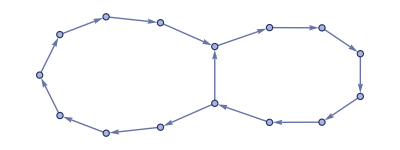
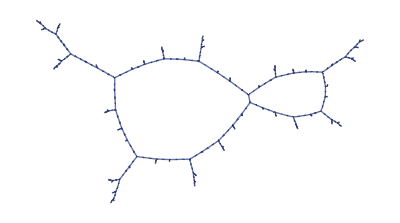
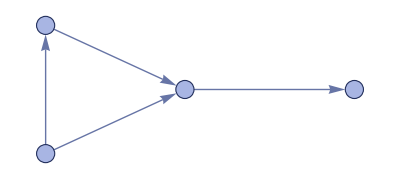
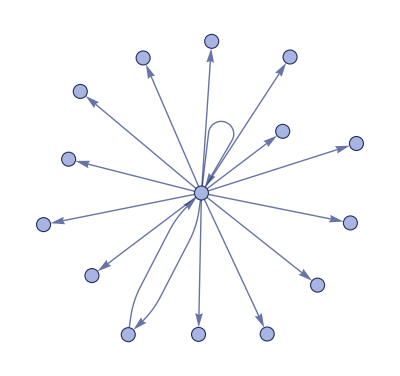
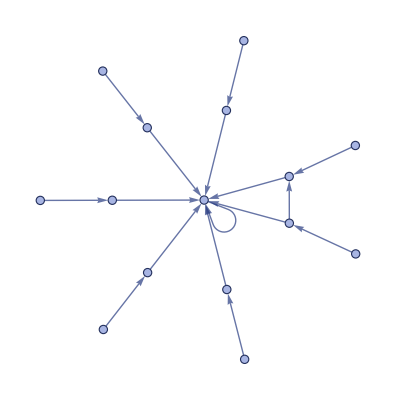
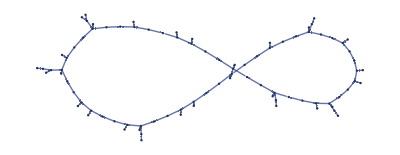
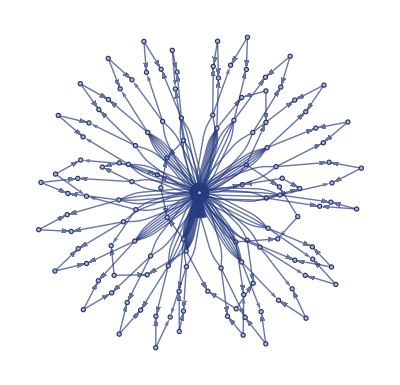
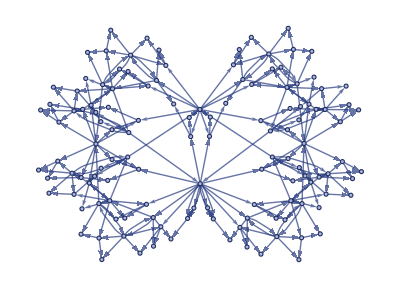
-Graphics--1.30996-Graphics--1.02383-Graphics--1.-Graphics--1.-Graphics--1.-Graphics--0.459432
-Graphics--1.30996-Graphics--0.960061-Graphics--0.895366-Graphics--0.43612-Graphics--0.297252-Graphics--0.0686656
-Graphics--1.30996-Graphics--1.02383-Graphics--0.841161-Graphics--0.112271-Graphics--0.0991386-Graphics--0.0991386
-Graphics--1.30996-Graphics--1.-Graphics--1.-Graphics--1.-Graphics--1.-Graphics--1.
-Graphics--1.30996-Graphics--1.11024-Graphics--1.-Graphics--1.-Graphics--0.459432-Graphics--0.459432

```mathematica
Column[Function[evolution, Row[Labeled[graphRule[First[#]], Last[#]]&/@evolution]]/@ evolutions]
```

```mathematica
evo = evolutions[[1]];
```

```mathematica
ListLinePlot[Function[evo,Callout[Last[#], graphRule[First[#]]]&/@evo]/@evolutions]
```

-Graphics-

## Mutate based on growth rate

```mathematica
(* average ratio between numbers of vertices on successive steps *)
(* 0 for non-connected final graphs *)
vertexGrowthRate[rule_]:=
With[{evolution=wm[rule, init, 7]},
If[ConnectedGraphQ[Graph[evolution["FinalState"]]],
N[Mean[
Ratios[
evolution["VertexCountList"]//
Function[nVertices, PadRight[nVertices, 6, Last@nVertices]]
]]],
0]
]
```

```mathematica
edgeGrowthRate[rule_]:=
With[{evolution=wm[rule, init, 7]},
If[ConnectedGraphQ[evolution["FinalState"]],
N[Mean[
Ratios[
evolution["EdgeCountList"]//
Function[nEdges, PadRight[nEdges, 6, Last@nEdges]]
]]],
0]
]
```

```mathematica
compareEvolutions[evolutions_]:=
Column[Function[evolution, Row[Labeled[graphRule[First[#]], Last[#]]&/@evolution]]/@ evolutions]
```

```mathematica
evolutions = ParallelMap[Function[rule, evolve[rule, vertexGrowthRate, 5]] , Table[rule, 5]];
```

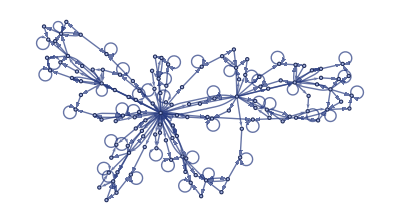
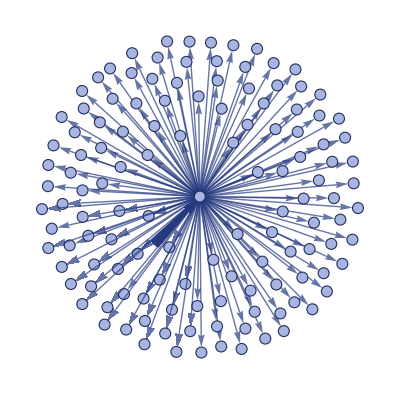
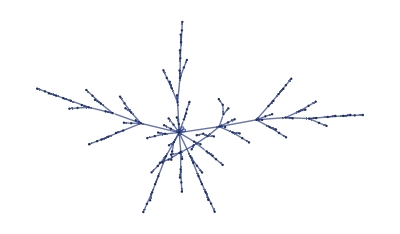
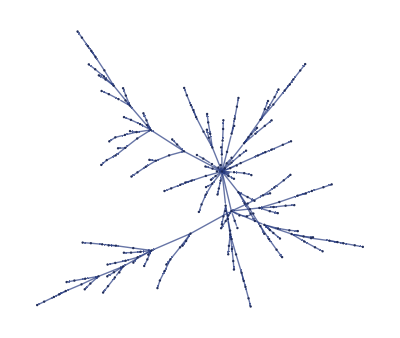
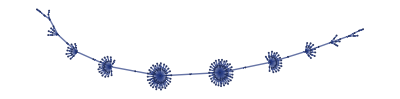
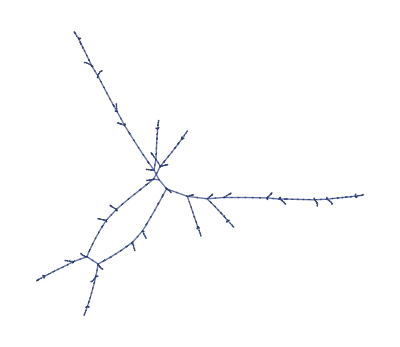
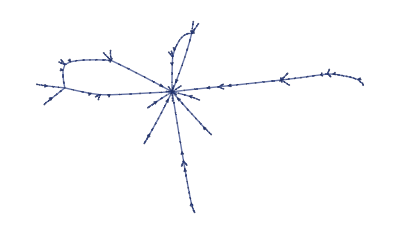
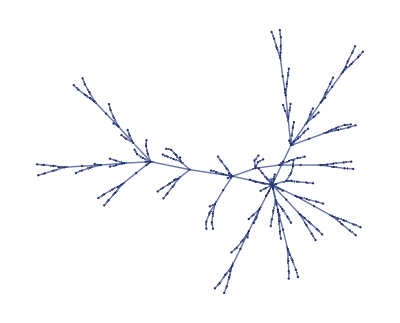
-Graphics-1.71492-Graphics-2.-Graphics-2.-Graphics-2.-Graphics-2.18271-Graphics-2.31502
-Graphics-1.71492-Graphics-2.31502-Graphics-2.31502-Graphics-2.31502-Graphics-2.31502-Graphics-2.31502
-Graphics-1.71492-Graphics-1.71492-Graphics-1.71492-Graphics-1.71492-Graphics-1.71492-Graphics-1.71492
-Graphics-1.71492-Graphics-1.71492-Graphics-1.71492-Graphics-1.71492-Graphics-1.71492-Graphics-1.71492
-Graphics-1.71492-Graphics-1.71492-Graphics-1.71492-Graphics-2.26122-Graphics-2.26122-Graphics-2.26122

```mathematica
compareEvolutions[evolutions]
```

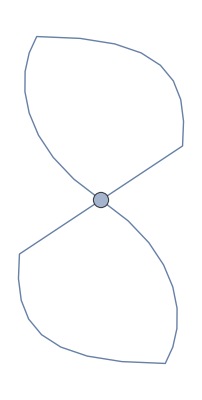
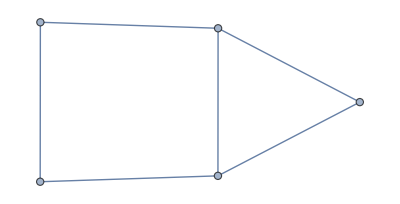
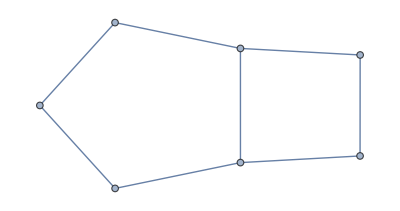
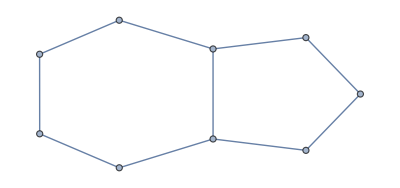
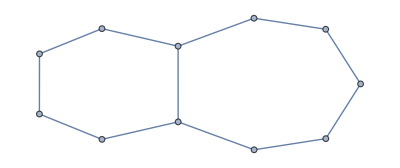
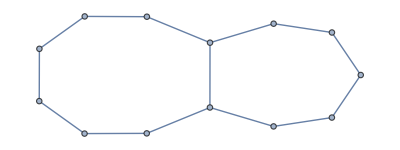
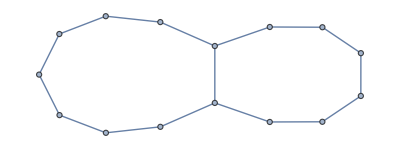
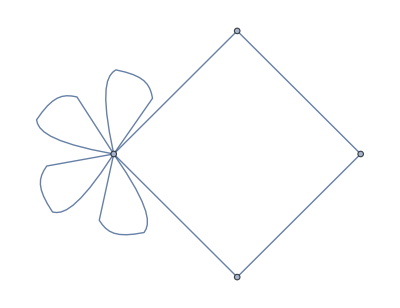
-Graphics-1-Graphics-3-Graphics-5-Graphics-7-Graphics-9-Graphics-11-Graphics-13-Graphics-15
-Graphics-1-Graphics-2-Graphics-4-Graphics-8-Graphics-16-Graphics-32-Graphics-64-Graphics-128
-Graphics-1-Graphics-2-Graphics-4-Graphics-8-Graphics-16-Graphics-32-Graphics-64-Graphics-128
-Graphics-1-Graphics-2-Graphics-4-Graphics-8-Graphics-16-Graphics-32-Graphics-64-Graphics-128
-Graphics-1-Graphics-2-Graphics-4-Graphics-8-Graphics-16-Graphics-32-Graphics-64-Graphics-128
-Graphics-1-Graphics-2-Graphics-4-Graphics-8-Graphics-16-Graphics-32-Graphics-64-Graphics-128

```mathematica
Column[Row/@Map[Labeled[Graph[#], Length[VertexList[#]]]&, Map[Function[rule, wm[rule, init, 7, "StatesList"]], First/@evolution], {2}]]
```

```mathematica
evo = evolve[rule, vertexGrowthRate, 5, 10];
```

```mathematica
Column[Row/@Map[Labeled[Graph[#], Length[VertexList[#]]]&, Map[Function[rule, wm[rule, init, 7, "StatesList"]], First/@evo], {2}]]
```

-Graphics-1-Graphics-3-Graphics-5-Graphics-7-Graphics-9-Graphics-11-Graphics-13-Graphics-15
-Graphics-1-Graphics-2-Graphics-4-Graphics-8-Graphics-16-Graphics-32-Graphics-64-Graphics-128
-Graphics-1-Graphics-2-Graphics-4-Graphics-8-Graphics-16-Graphics-32-Graphics-64-Graphics-128
-Graphics-1-Graphics-2-Graphics-4-Graphics-8-Graphics-16-Graphics-32-Graphics-64-Graphics-128
-Graphics-1-Graphics-2-Graphics-4-Graphics-8-Graphics-16-Graphics-32-Graphics-64-Graphics-128
-Graphics-1-Graphics-2-Graphics-4-Graphics-8-Graphics-16-Graphics-32-Graphics-64-Graphics-128

## TODO

#### Issues

Find suspension cause

#### New fitness functions

Rules whose dimensions stabilize

Different dimension estimates

Edge to vertex ratios

Measure of repetition / complexity

#### Utilities

Track evolution progress

Plot fitness over time

Inset with state plot

Show states across time

Show change in rules across evolution

Plot in rule space

#### Rule Mutations

Add and remove vertices

Add and remove edges

Add and remove replacements

Crossover